```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A=({{0, -ⅈ}, {-ⅈ, 0}}); W[a_]:=({{Exp[a], 0}, {0, Exp[-a]}});U[a_,b_]:=FullSimplify[b-a^2/4-D[a,x]/2];
```

Function[x,-(x+δ^2+3/(4 x^2))]

{{x→-0.90856},{x→0.45428+0.786836 ⅈ},{x→0.45428-0.786836 ⅈ}}

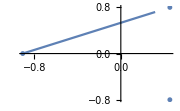
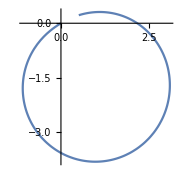
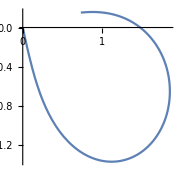

3.46945×10^-18+1.8138 ⅈ

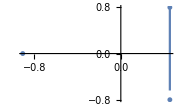
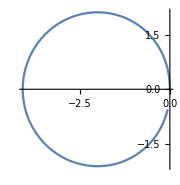
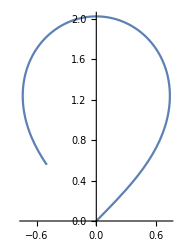

5.39499×10^-16+1.8138 ⅈ

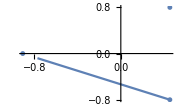
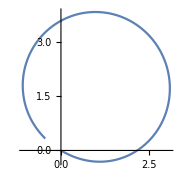
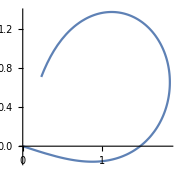

-4.16334×10^-17-1.8138 ⅈ

```mathematica
δ=0;Q=Function[x,-(x+δ^2+3/(4 x^2))] 
zeros=NSolve[Q[x]==0,x]

ab=Function[t,(x/.zeros[[1]])+((x/.zeros[[2]])-(x/.zeros[[1]]))t];
abVal=Function[t,√Q[ab[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(ab[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[ab[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[abVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(abVal[t]ab'[t]),{t,0,1}]

bc=Function[t,(x/.zeros[[2]])+((x/.zeros[[3]])-(x/.zeros[[2]]))t];
bcVal=Function[t,Piecewise[{{√Q[bc[t]],Im[Q[bc[t]]]>=0},{-√Q[bc[t]],Im[Q[bc[t]]]<0}}]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(bc[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[bc[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[bcVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(bcVal[t]bc'[t]),{t,0,1}]

ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(ca[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[ca[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[caVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}]
```

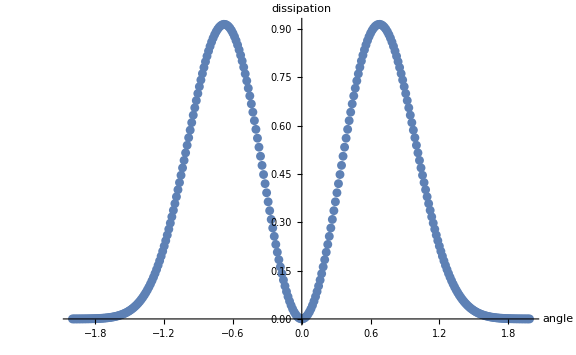

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
For[δ=begining,δ<end,δ+=(end-begining)/nstep,
Q=Function[x,-(x+δ^2+3/(4 x^2))];
zeros=NSolve[Q[x]==0,x];
ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];
CA=NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}];
Amp=FullSimplify[S[-ⅈ].W[CA].S[2ⅈ*Exp[2CA0]].({{1}, {0}})];
Dissipation=Append[Dissipation,{δ,1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2}];
]; Clear[Amp];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation},ImageSize->Large]
```

{{x→-0.930796},{x→0.467026+0.766806 ⅈ},{x→0.467026-0.766806 ⅈ},{x→-0.00164165+0.18517 ⅈ},{x→-0.00164165-0.18517 ⅈ},{x→0.0311856},{x→-0.0311578}}

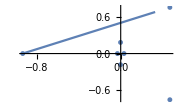
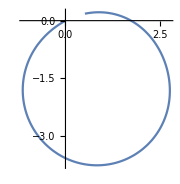
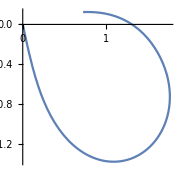

0.0263584+1.8284 ⅈ

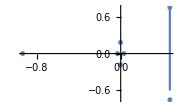
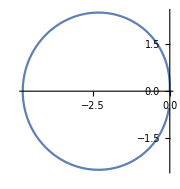
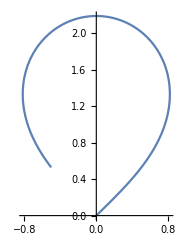

-7.76115×10^-15+1.78489 ⅈ

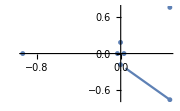
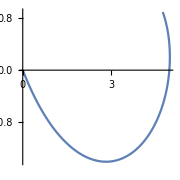
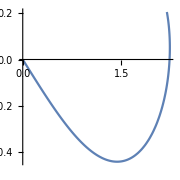

-0.853602-0.468419 ⅈ

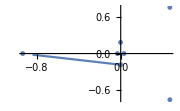
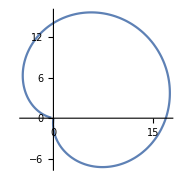
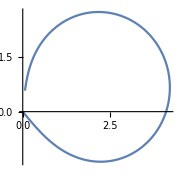

0.87996-1.35998 ⅈ

```mathematica
δ=0;u=0.0001; a=100*u; Q=Function[x,(4 a^3 x+2 a x^2 (-5+6 x^3-4 √u δ+4 x^2 δ^2)-x^4 (3-8 √u δ+4 x^2 (x+δ^2))+a^2 (1-4 x^2 (3 x+δ^2)))/(4 (-a x+x^3)^2)];zeros=NSolve[Q[x]==0,x]
ab=Function[t,(x/.zeros[[1]])+((x/.zeros[[2]])-(x/.zeros[[1]]))t];
abVal=Function[t,√Q[ab[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(ab[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[ab[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[abVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(abVal[t]ab'[t]),{t,0,1}]

bc=Function[t,(x/.zeros[[2]])+((x/.zeros[[3]])-(x/.zeros[[2]]))t];
bcVal=Function[t,Piecewise[{{√Q[bc[t]],Im[Q[bc[t]]]>=0},{-√Q[bc[t]],Im[Q[bc[t]]]<0}}]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(bc[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[bc[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[bcVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(bcVal[t]bc'[t]),{t,0,1}]

cd=Function[t,(x/.zeros[[3]])+((x/.zeros[[5]])-(x/.zeros[[3]]))t];
cdVal=Function[t,√Q[cd[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(cd[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[cd[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[cdVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(cdVal[t]cd'[t]),{t,0,1}]

da=Function[t,(x/.zeros[[5]])+((x/.zeros[[1]])-(x/.zeros[[5]]))t];
daVal=Function[t,√Q[da[t]]];

Show[ListPlot[Table[{Re[x/.zeros[[i]]],Im[x/.zeros[[i]]]},{i,1,Length[zeros]}]],ParametricPlot[(da[t])//{Re[#],Im[#]}&,{t,0,0.9}],ImageSize->Small];
ParametricPlot[Q[da[t]]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
ParametricPlot[daVal[t]//{Re[#],Im[#]}&,{t,0,0.9},PlotRange->Full,ImageSize->Small];
Row[{%%%,%%,%}]
NIntegrate[ⅈ(daVal[t]da'[t]),{t,0,1}]
```

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 2 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.{}⟦2⟧

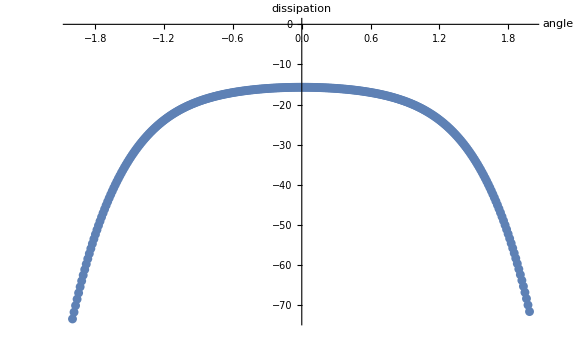

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
u=0.0000001; a=100*u;

δ=0;
Q=Function[x,(4 a^3 x+2 a x^2 (-5+6 x^3-4 √u δ+4 x^2 δ^2)-x^4 (3-8 √u δ+4 x^2 (x+δ^2))+a^2 (1-4 x^2 (3 x+δ^2)))/(4 (-a x+x^3)^2)];
zeros=NSolve[Q[x]==0,x];
cd=Function[t,(x/.zeros[[3]])+((x/.zeros[[5]])-(x/.zeros[[3]]))t];
cdVal=Function[t,√Q[cd[t]]];
CD=NIntegrate[ⅈ(cdVal[t]cd'[t]),{t,0,1}];

da=Function[t,(x/.zeros[[5]])+((x/.zeros[[1]])-(x/.zeros[[5]]))t];
daVal=Function[t,√Q[da[t]]];
DA=NIntegrate[ⅈ(daVal[t]da'[t]),{t,0,1}];
Amp=FullSimplify[S[-ⅈ].W[DA].S[x].W[CD].S[2ⅈ*Exp[2CA0]].({{1}, {0}})];
1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2;
ax=x/.Solve[%==0,{x}][[2]]

For[δ=begining,δ<end,δ+=(end-begining)/nstep,
Q=Function[x,(4 a^3 x+2 a x^2 (-5+6 x^3-4 √u δ+4 x^2 δ^2)-x^4 (3-8 √u δ+4 x^2 (x+δ^2))+a^2 (1-4 x^2 (3 x+δ^2)))/(4 (-a x+x^3)^2)];
zeros=NSolve[Q[x]==0,x];
cd=Function[t,(x/.zeros[[3]])+((x/.zeros[[5]])-(x/.zeros[[3]]))t];
cdVal=Function[t,√Q[cd[t]]];
CD=NIntegrate[ⅈ(cdVal[t]cd'[t]),{t,0,1}];

da=Function[t,(x/.zeros[[5]])+((x/.zeros[[1]])-(x/.zeros[[5]]))t];
daVal=Function[t,√Q[da[t]]];
DA=NIntegrate[ⅈ(daVal[t]da'[t]),{t,0,1}];
Amp=FullSimplify[S[-ⅈ].W[DA].S[ax].W[CD].S[2ⅈ*Exp[2CA0]].({{1}, {0}})];
Dissipation=Append[Dissipation,{δ,1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2}];
]; Clear[Amp];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation},ImageSize->Large]
```

```mathematica
CW=FullSimplify[S[β21]ᵀ.W[-AB].S[β32]ᵀ.S[β54].W[-BC].S[β65].S[β87]ᵀ.W[AB*].S[β98]ᵀ]
CCW=FullSimplify[S[α89].W[-AB*].S[α78].S[α56]ᵀ.W[BC].S[α45]ᵀ.S[α23].W[AB].S[α12]]
```

```mathematica
Det[({{1, Log[z], 1}, {1, Log[z]-2π*ⅈ, -ⅈ(CW[[2,1]]+CW[[1,1]]Exp[4/3 z^(3/2)])}, {1, Log[z]+2π*ⅈ, ⅈ(CCW[[2,1]]+CCW[[1,1]]Exp[4/3 z^(3/2)])}})]//FullSimplify
```

```mathematica
Det[({{1, Log[z], 1}, {1, Log[z]-2π*ⅈ, -ⅈ(CW[[1,2]]+CW[[2,2]]Exp[-4/3 z^(3/2)])}, {1, Log[z]+2π*ⅈ, ⅈ(CCW[[1,2]]+CCW[[2,2]]Exp[-4/3 z^(3/2)])}})]//FullSimplify
```

```mathematica
Solve[{2 ⅈ ⅇ^(AB+BC+Conjugate[AB])+ⅇ^(2 (BC+Conjugate[AB])) α12 α45 α78+ⅇ^(2 Conjugate[AB]) α12 (1+α56 α78)+ⅇ^(2 BC) α12 α45 α89+ⅇ^(2 (AB+BC)) (1+α23 α45) α89+α12 α56 α89+ⅇ^(2 AB) α23 α56 α89+ⅇ^(4 Re[AB]) (α23+α23 α56 α78-β54)+ⅇ^(2 (AB+BC+Conjugate[AB])) (α78+α23 α45 α78-β65)==0,
ⅇ^(2 BC) α12 α45+ⅇ^(2 (AB+BC)) (1+α23 α45)+α12 α56+ⅇ^(2 AB) α23 α56-ⅇ^(4 Re[AB]) β21 β54-ⅇ^(2 Conjugate[AB]) (1+β32 β54)-ⅇ^(2 BC+4 Re[AB]) β21 β65-ⅇ^(2 BC+2 Conjugate[AB]) β32 β65==0,
-ⅇ^(2 (AB+BC))+ⅇ^(2 Conjugate[AB])+ⅇ^(2 (BC+Conjugate[AB])) α45 α78+ⅇ^(2 Conjugate[AB]) α56 α78+ⅇ^(2 BC) α45 α89+α56 α89-ⅇ^(2 AB) β54 β87-ⅇ^(2 (AB+BC)) β65 β87-ⅇ^(4 Re[AB]) β54 β98-ⅇ^(2 (AB+BC+Conjugate[AB])) β65 β98==0,
-2 ⅈ ⅇ^(AB+BC+Conjugate[AB])-α56+β87+ⅇ^(2 AB) β21 β54 β87+β32 β54 β87+ⅇ^(2 (AB+BC)) β21 (1+β65 β87)+ⅇ^(2 BC) (-α45+β32+β32 β65 β87)+ⅇ^(4 Re[AB]) β21 β54 β98+ⅇ^(2 Conjugate[AB]) (1+β32 β54) β98+ⅇ^(2 (AB+BC+Conjugate[AB])) β21 β65 β98+ⅇ^(2 (BC+Conjugate[AB])) β32 β65 β98==0}/.{AB->-BA,BC->-CB},{α12,α23,α45,α56,α78,α89,β98,β87,β65,β54,β32,β21}]
```

$Aborted

```mathematica
δ=0;
Q=Function[x,(4 a^3 x+2 a x^2 (-5+6 x^3-4 √u δ+4 x^2 δ^2)-x^4 (3-8 √u δ+4 x^2 (x+δ^2))+a^2 (1-4 x^2 (3 x+δ^2)))/(4 (-a x+x^3)^2)];
zeros=NSolve[Q[x]==0,x];
cd=Function[t,(x/.zeros[[3]])+((x/.zeros[[5]])-(x/.zeros[[3]]))t];
cdVal=Function[t,√Q[cd[t]]];
CD=NIntegrate[ⅈ(cdVal[t]cd'[t]),{t,0,1}];

da=Function[t,(x/.zeros[[5]])+((x/.zeros[[1]])-(x/.zeros[[5]]))t];
daVal=Function[t,√Q[da[t]]];
DA=NIntegrate[ⅈ(daVal[t]da'[t]),{t,0,1}];
Amp=FullSimplify[S[-ⅈ].W[DA].S[x].W[CD].S[2ⅈ*Exp[2CA0]].({{1}, {0}})];
1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2
Solve[%==0,{x}]
```

1-0.948649 Abs[(0.904554-0.179483 ⅈ)+(0.110973+0.137447 ⅈ) x]^2

{{x→-6.07719+9.14432 ⅈ},{x→1.22491+0.100236 ⅈ}}

{{a1→1.34414×10^6+810098. ⅈ}}

```mathematica
a1/.{a1->4.465998883552968*^-92 ((2.405593497172002*^90-3.2720511664662956*^90 ⅈ) a2-(2.053943220484505*^91-1.1629953486174001*^91 ⅈ) a3-1. √((-4.8480200123786235*^182+2.745073314670504*^182 ⅈ)+(4.590533290215775*^165-2.7803872939998433*^164 ⅈ) a2^2-(1.4749016324914095*^166+2.1718449370182946*^166 ⅈ) a2 a3-(5.542973102552143*^166+5.365082922567058*^165 ⅈ) a3^2))}/.a2->-ⅈ/.a3->-ⅈ
```

0.104705-0.20949 ⅈ

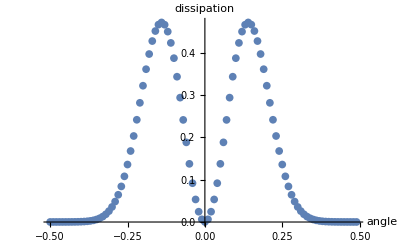

```mathematica
Reflection={};
Dissipation={};
Θbegining=-0.5;Θend=0.5;Θnstep=100;
ProgressIndicator[Dynamic[(θ-Θbegining)/(Θend-Θbegining)]]
For[θ=Θbegining,θ<Θend,θ+=(Θend-Θbegining)/Θnstep,
sol = GeneralLinearAnizatropy[0.000001,0,30,θ,π/2,{0,1}];
reflection = (sol[[5]][[2]])/(sol[[4]][[2]]);
Reflection=Append[Reflection,{Sin[θ]*30^(1/3),reflection}];
Dissipation = Append[Dissipation,{θ,1-Abs[reflection]^2}];
];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation}]
```

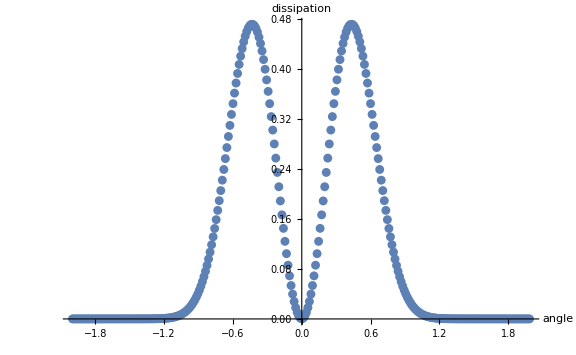

```mathematica
Dissipation={};
Stokes={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
a89=-ⅈ;
For[δ=begining,δ<end,δ+=(end-begining)/nstep,
Q=Function[x,-(x+δ^2+3/(4 x^2))];
zeros=NSolve[Q[x]==0,x];
ca=Function[t,(x/.zeros[[3]])+((x/.zeros[[1]])-(x/.zeros[[3]]))t];
caVal=Function[t,√Q[ca[t]]];
CA=NIntegrate[ⅈ(caVal[t]ca'[t]),{t,0,1}];
(*===========================*)
sol = GeneralLinearAnizatropy[0.000001,0,30,ArcSin[30^(-1/3)*δ],π/2,{0,1}];
reflection = (sol[[5]][[2]])/(sol[[4]][[2]]);
a78=(reflection-a89)*Exp[2CA];
Stokes=Append[Stokes,{δ,a78}];
Amp=FullSimplify[S[-ⅈ].W[CA].S[a78].({{1}, {0}})];
Dissipation=Append[Dissipation,{δ,1-Abs[(Amp[[2]][[1]])/(Amp[[1]][[1]])]^2}];
]; Clear[Amp];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{angle,dissipation},ImageSize->Large]
```

```mathematica
ListPointPlot3D[Table[{Re[Stokes[[i,2]]],Im[Stokes[[i,2]]],Stokes[[i,1]]},{i,1,Length[Stokes]}],PlotRange->Full,AxesLabel->{Re,Im,delta}]
```

-Graphics3D-

```mathematica
sol
```

{{{1-((0.125-1.25×10^-7 ⅈ) (9-x^2))/(1-8.22526×10^-20 x^40.),0.+0. ⅈ,0},{0.+0. ⅈ,1-((0.125-1.25×10^-7 ⅈ) (9-x^2))/(1-8.22526×10^-20 x^40.),0},{0,0,1-((0.125-1.25×10^-7 ⅈ) (9-x^2))/(1-8.22526×10^-20 x^40.)}},{30 √(1-22201/(5625 30^(2/3))),(149 2^(2/3))/(5 15^(1/3)),0},{InterpolatingFunction[{{-6., 6.}}, <>],InterpolatingFunction[{{-6., 6.}}, <>],InterpolatingFunction[{{-6., 6.}}, <>],InterpolatingFunction[{{-6., 6.}}, <>]},{0,-2.80488×10^30-7.40984×10^30 ⅈ},{0,1.965×10^30+7.67514×10^30 ⅈ},{0,1},0.0000329681}

```mathematica
sol[[4]]
```

{0,-2.80488×10^30-7.40984×10^30 ⅈ}

```mathematica
{sol[[4]][[1]],sol[[4]][[2]],0}×({0,0,1}×{sol[[4]][[1]],sol[[4]][[2]],0})
```

{0.,0.,-4.70384×10^61+4.15675×10^61 ⅈ}